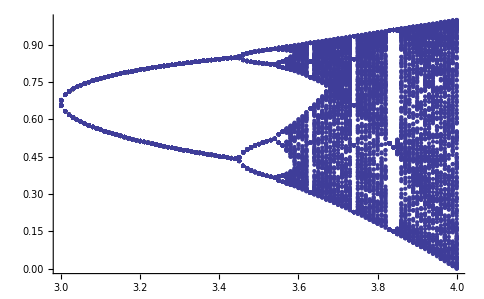

```mathematica
Show[Table[Subscript[x, 0]=0.1;f[x_]=a x (1-x);ListPlot[Table[{a,Nest[f,Subscript[x, 0],i]},{i,400,600}]],{a,3,4,0.01}]]
```

```mathematica
Chaos
```

```mathematica
Manipulate[
Clear[x,y,z];
sol=NDSolve[{x'[t]==-y[t]-z[t],y'[t]==x[t]+a y[t],z'[t]==2+z[t](x[t]-4),x[0]==0.5,y[0]==0.5,z[0]==0.5},{x,y,z},{t,0,1000},MaxSteps->50000];
{x,y,z}={x,y,z}/.sol[[1]];
ParametricPlot3D[Evaluate[{x[t],y[t],z[t]}],{t,500,1000}]
,{a,0.3,0.5,0.001}]
```

```mathematica
a=0.379;
While[a≤0.51,
Clear[x,y,z];
sol=NDSolve[{x'[t]==-y[t]-z[t],y'[t]==x[t]+a y[t],z'[t]==2+z[t](x[t]-4),x[0]==0.5,y[0]==0.5,z[0]==0.5},{x,y,z},{t,0,1000},MaxSteps->50000];
{x,y,z}={x,y,z}/.sol[[1]];
Print[ParametricPlot3D[Evaluate[{x[t],y[t],z[t]}],{t,500,1000},PlotRange->Full]];
a=a+0.001]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

«129 more identical outputs»